EarthShadow v1.1 (21/11/2016) - Examples

```mathematica
Quit[];
```

## Loading the EarthShadow Package

```mathematica
SetDirectory[NotebookDirectory[]];
Get["EarthShadow`"]
```

The EarthShadow package allows you to calculate the effects of DM-scattering in the Earth.
Send corrections/suggestions to bradkav@gmail.com.
To get a list of available functions, type: ?EarthShadow`*

```mathematica
?EarthShadow`*
```

EarthShadow tends to complain about integrals a lot, so let’s shut it up!

```mathematica
Off[NIntegrate::maxp];
```

## Scattering probabilities

The function pscat allows you to calculate the average probability of DM scattering in the Earth:

```mathematica
mDM = 300; (*GeV*)
operator = 1; (*Standard SI*)
coupling = 0.0001; (*1/GeV^2*)

pscat[mDM, operator, coupling]
```

1.00012

We could also fix the coupling in terms of the cross section (See Eq. 4.2 of the paper):

```mathematica
xsec2coupling[σ_, mx_]:=
(
(*Coupling in 1/GeV^2 from cross section in cm^2*)
μ = 0.9315*mx/(mx + 0.9315);
2*5.06*^13*Sqrt[π*σ]/μ
)
```

Now we just fix the DM-proton cross section and check the scattering probability:

```mathematica
pscat[mDM, operator, xsec2coupling[10^-40, mDM]]
```

0.980652

For some of the benchmarks which have already been calculated, there are some tables which specify the coupling which gives you a given value of the scattering probability (as a function of Log10[mDM]). These tables are in the ‘results’ folder. Let’s look at the p = 10% couplings (‘ps=0.10’):

```mathematica
pscatTable = Import[NotebookDirectory[]<>"../results/pscat/couplings_op=1_ps=0.10.dat", "Table"];
```

The first column is Log10 of the DM mass and the second column is the coupling required for 10% scattering. The coupling required for a 5 GeV particle is then:

```mathematica
c10 = Interpolation[pscatTable][Log10[mDM]]
```

0.000045298

And if we’ve done everything right, this should in fact give us the correct scattering probability:

```mathematica
pscat[mDM, operator, c10]
```

0.0994617

Close enough...

## Distribution of deflection angles

We can calculate the probability distributions for the angle α, the deflection angle of the DM particle after scattering. Let’s look at scattering with Oxygen, for a light-ish DM particle. The iso values for the different Earth elements are in Isotopes.txt in the ‘data’ folder:

```mathematica
mDM = 5;
iso = 1; (*Oxygen*)
v0 = 220; (*km/s*)
```

Let’s plot for a selection of operators:

```mathematica
OpList = {1, 3, 5, 8, 12,15};
```

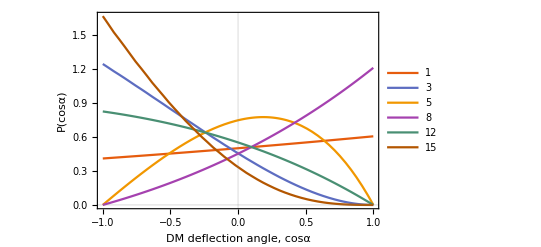

```mathematica
Plot[Evaluate[Table[Pcαplus[cα, mDM, iso,op, v0], {op,OpList}]], {cα,-1,1},PlotTheme->"Scientific", FrameLabel->{"DM deflection angle, cosα", "P(cosα)", "Scattering with Oxygen - m_χ = "<> ToString[mDM] <> " GeV"},BaseStyle->{FontSize->16}, PlotLegends->OpList]
```

## Perturbed speed distributions

Now to calculate the perturbed speed distribution. Let’s pick some random parameter values, and focus on 10% scattering (see the ‘Scattering Probabilities’ section):

```mathematica
mDM = 5;
operator = 1;
c10 = 0.0000453;
```

The full distribution is given by the sum of SpeedDistFree, SpeedDistAttenuation and SpeedDistDeflection.

The free speed distribution is easy:

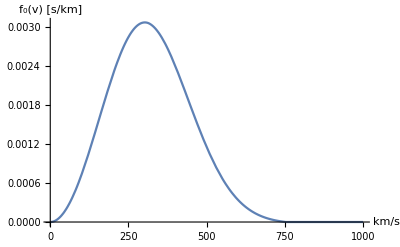

```mathematica
Plot[SpeedDistFree[v], {v, 0, 1000}, AxesLabel->{"km/s", "f_0(v) [s/km]"}]
```

The attenuated speed distribution depends on the angle γ (defined in Fig. 1 of the paper). γ = 0 means that particles cross most of the Earth to get to the detector, while γ = π means that they appear to come from directly overhead, and cross very little of the Earth. Let’s just pick γ = π/2 for now.

```mathematica
γ = π/2;
```

For (say) v = 250 km/s, attenuation reduces the speed distribution by:

```mathematica
SpeedDistAttenuation[250, γ, mDM, operator, c10]
```

-0.0000663017

Similarly, the enhancement due to deflection is:

```mathematica
SpeedDistDeflection[250, γ, mDM, operator, c10]
```

0.000139532

Some of these values have already been tabulated in the ‘results’ folder for a few masses and operators. To generate more tables, you can use the following code:

```mathematica
CalcFullSpeedDist[op_, mx_, γoverpi_, ps_:0.1]:=
( 
 γ = γoverpi*π;

(*Calculate the scattering probabilities*)
pscatinterp = Interpolation[Import[NotebookDirectory[] <> "../results/pscat/couplings_op=" <> ToString[op] <>"_ps="<> ToString[NumberForm[ps,{5,2}]]<> ".dat", "Table"]];
c0 = pscatinterp[Log10[mx]];

(*Calculate speed distributions over a grid*)
vlist =  Sort[Flatten[{Range[1, 751, 25], 736, 753}]];

(*Free distribution*)
ffree = Table[SpeedDistFree[v], {v,vlist}];

(*Loss due to attenuation*)
PrintTemporary["  Calculating f_A(v)-f_0(v)..."];
Quiet[fpert1 =Table[PrintTemporary["    v = " <> ToString[v] <> " km/s"];SpeedDistAttenuation[v, γ, mx, op, c0],{v, vlist}];];

(*Enhancement due to deflection*)
PrintTemporary["  Calculating f_D(v)..."];
Quiet[fpert2 =Table[PrintTemporary["    v = " <> ToString[v] <> " km/s"];SpeedDistDeflection[v, γ, mx, op, c0],{v, vlist}];];

(*Tabulate and output*)
results = Table[{vlist[[i]],ffree[[i]], fpert1[[i]], fpert2[[i]]}, {i, Length[vlist]}];

Export[NotebookDirectory[] <> "../results/Speeddist_op=" <> ToString[op] <> "_mx="<> ToString[NumberForm[mx,{5,2}]] <> "_gam=" <>ToString[NumberForm[γoverpi,{5,2}]]<>"_ps="<> ToString[NumberForm[ps,{5,2}]]<> ".dat", results];
)
```

Here, γoverpi is...erm... the value of γ divided by π. To use this code, you have to have the scattering probabilities tabulated already in the results folder. Note that the above function is likely to take 5+ minutes to run.

```mathematica
(*CalcFullSpeedDist[operator, mDM, 0.5]*)
```

## Plotting speed distributions

You can plot some of the tabulated speed distributions in the results folder using the following function. Here, coeffA and coeffD multiply the attenuation and deflection contributions, so you can switch them on and off easily. You might just need to let Mathematica know where to find the results tables:

```mathematica
ResultsDir = NotebookDirectory[] <> "../results/LowMass/";
```

```mathematica
PlotSpeedDists[op_, mx_, γoverpi_, coeffA_:1, coeffD_:1, ps_:0.10]:=
(
(*Check that the file exists*)
mstring = ToString[NumberForm[mx,{5,2}]];
filename = ResultsDir <> "Speeddist_op=" <> ToString[op] <> "_mx=" <> mstring <> "_gam=" <> ToString[NumberForm[γoverpi,{5,2}]]<>"_ps="<> ToString[NumberForm[ps,{5,2}]]<> ".dat";
If[Not[FileExistsQ[filename]], Print["Error: file '" <> filename <> "' not found..."];
 Return[-1;]; ];

(*Load the data file*)
SpeedDist = Import[filename, "Table"];
Nv =Length[SpeedDist[[All,1]]];

(*Calculate free + perturbed distributions, and the ratio*)
ffree = Interpolation[Table[{SpeedDist[[i,1]] , SpeedDist[[i,2]] }, {i,Nv}], InterpolationOrder->1];

fpert = Interpolation[Table[{SpeedDist[[i,1]] , SpeedDist[[i,2]] +coeffA*SpeedDist[[i,3]]+coeffD*SpeedDist[[i,4]]}, {i,Nv}],InterpolationOrder->1];

fratio = Interpolation[Table[{SpeedDist[[i,1]] , (SpeedDist[[i,2]] + coeffA*SpeedDist[[i,3]]+coeffD*SpeedDist[[i,4]])/SpeedDist[[i,2]]}, {i,Nv}],InterpolationOrder->1];

(*Do some plotting*)
p1 = Plot[{ffree[v], fpert[v]},{v, 1, 753}, PlotTheme->"Scientific",FrameLabel->{"v / km s^-1 ", "f̃(v,γ)/ 10^-3 km^-1 s"},PlotLegends->Placed[LineLegend[{"Free", "Perturbed"}],{0.75, 0.75}],FrameStyle->Directive[15], ImageSize-> 400,BaseStyle->{FontSize->12}, FrameStyle->Black,LabelStyle->Black, PlotLabel->"m_χ = " <> ToString[mx] <> " GeV;   op = " <> ToString[op] <> ";   γ = " <> ToString[γoverpi] <> " π ;   p_scat = 10%" , ImagePadding->{{75,10},{0,10}}];
p2 = ListPlot[Table[{v,fratio[v]},{v,SpeedDist[[All,1]] }], PlotTheme->"Scientific",FrameLabel->{"v/ km s^-1", "f̃(v,γ)/f_O(v)"},FrameStyle->Directive[15], ImageSize-> 400, BaseStyle->{FontSize->12}, FrameStyle->Black, PlotStyle->Black,LabelStyle->Black, GridLines->{{0},{1}}, ImagePadding->{{75,10},{50,0}}, AspectRatio->0.4, Joined->True, InterpolationOrder->1];

max=Max@Abs@Last[PlotRange/.AbsoluteOptions[p2,PlotRange]];
min=Min@Abs@Last[PlotRange/.AbsoluteOptions[p2,PlotRange]];
diff = Sqrt[Max[(max-1)^2, (1-min)^2]];
Column[{p1,Show[p2,PlotRange->{{0, 753}, {1-diff, 1+diff}}]}, Spacings->0]
)
```

And here’s an example:

```mathematica
operator = 1;
mDM = 0.5;
γ1 = π/2;
```

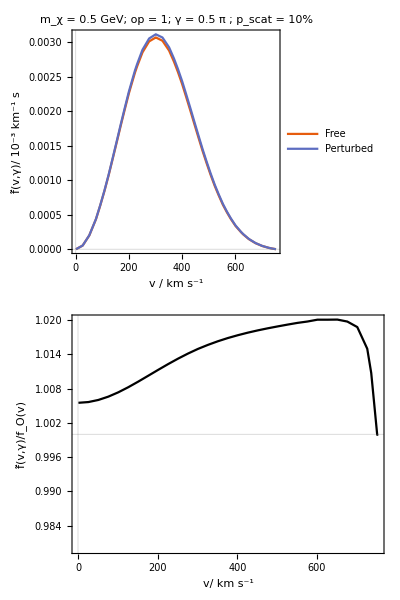

```mathematica
PlotSpeedDists[operator, mDM, N[γ1/π]]
```